```mathematica
data1=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0000500.dat","Table"];
data2=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0001000.dat","Table"];
data3=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0001500.dat","Table"];
data4=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0002000.dat","Table"];
data5=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0002500.dat","Table"];
data6=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0003000.dat","Table"];
data7=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0003500.dat","Table"];
data8=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0004000.dat","Table"];
data9=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0004500.dat","Table"];
data10=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0005000.dat","Table"];
data11=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0005500.dat","Table"];
data12=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0006000.dat","Table"];
data13=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0006500.dat","Table"];
data14=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0007000.dat","Table"];
data15=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0007500.dat","Table"];
data16=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0008000.dat","Table"];
data17=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0008500.dat","Table"];
data18=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0009000.dat","Table"];
data19=Import["/home/patrick/git/TwoDimTubes/2WellTubes-T0.15-pos0009500.dat","Table"];
aveData[n_]:=Sum[ToExpression["data"<>ToString[i]],{i,1,n}]/n;
Dimensions[data1]
dSets=19;
```

{20001,12}

## Data Structure

Structure of the plots:
1) x position
2) y position
3) x mean
4) y mean
5) xx covariance
6) yy covariance
7) xy covariance
8) dD_kl/dm_x
9) dD_kl/dm_y
10) dD_kl/dB_xx
11) dD_kl/dB_yy
12) dD_kl/dB_xy

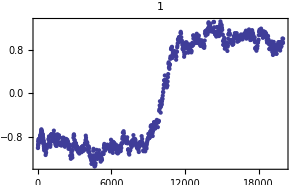
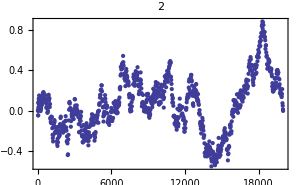
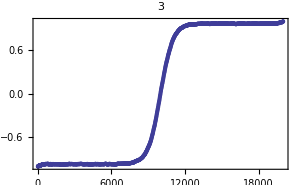
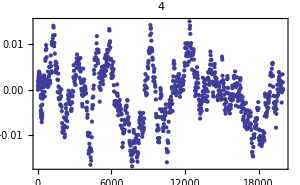
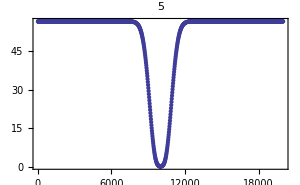
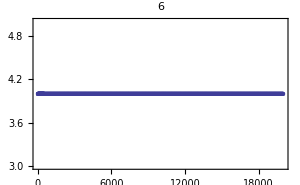
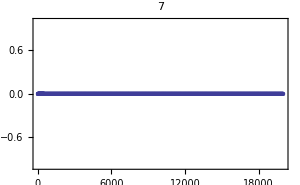
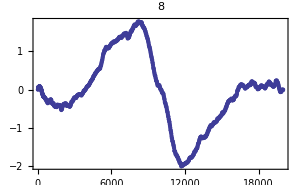

```mathematica
Table[ListPlot[data1[[All,i]],MaxPlotPoints->1000,PlotRange->All,ImageSize->300,PlotLabel->ToString[i],Frame->True],{i,1,12}]
```

## dD_kl/dm_x evolution

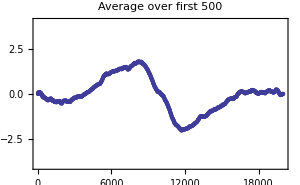
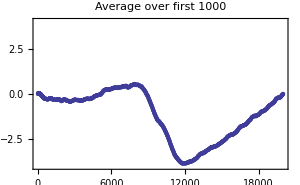
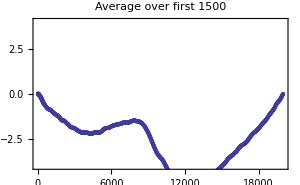
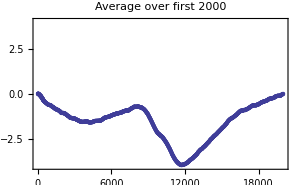
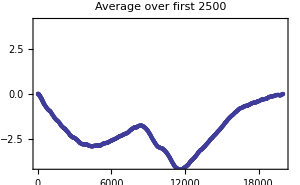
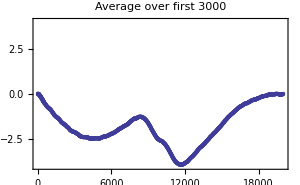
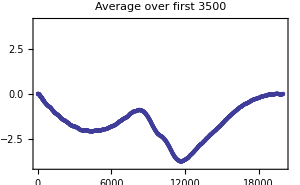
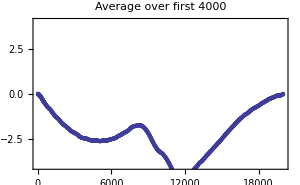

```mathematica
Table[ListPlot[aveData[n][[All,8]],MaxPlotPoints->1000,ImageSize->300,PlotRange->{{0,20000},{-4,4}},Frame->True,PlotLabel->"Average over first "<>ToString[n*500]],{n,1,dSets}]
```

## dD_kl/dm_y evolution

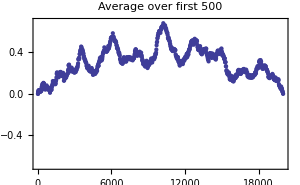
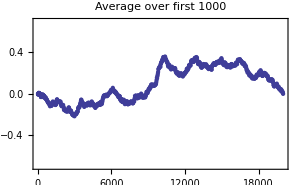
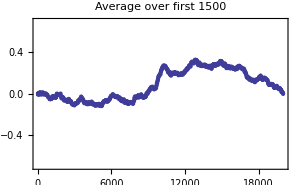
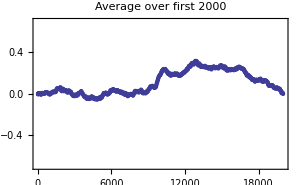
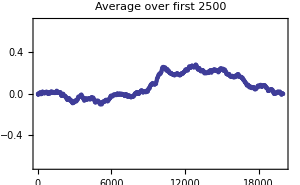
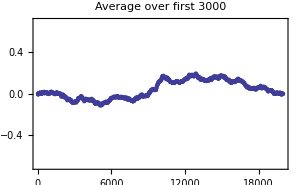
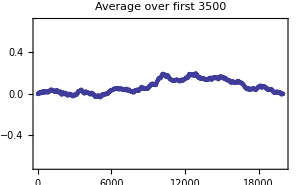
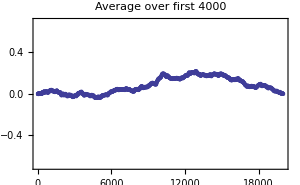

```mathematica
Table[ListPlot[aveData[n][[All,9]],MaxPlotPoints->1000,ImageSize->300,PlotRange->{{0,20000},{-0.7,0.7}},Frame->True,PlotLabel->"Average over first "<>ToString[n*500]],{n,1,dSets}]
```

## dD_kl/dB_xx evolution

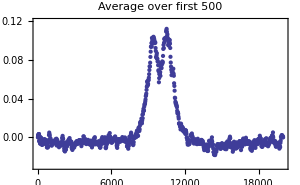
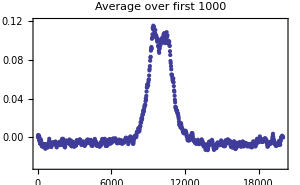
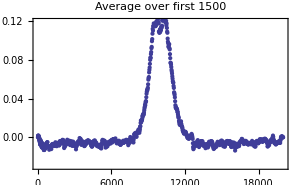
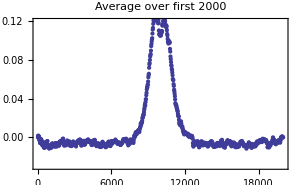
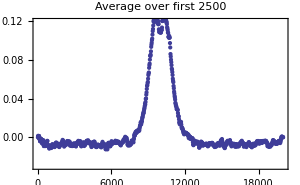
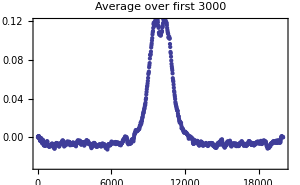
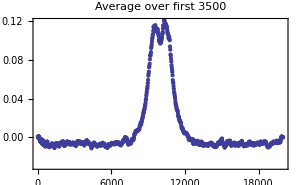
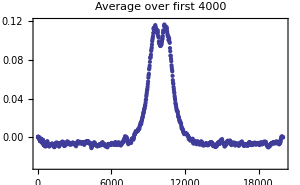

```mathematica
Table[ListPlot[aveData[n][[All,10]],MaxPlotPoints->1000,ImageSize->300,PlotRange->{{0,20000},{-0.03,0.12}},Frame->True,PlotLabel->"Average over first "<>ToString[n*500]],{n,1,dSets}]
```

## Testing Steepest Descent

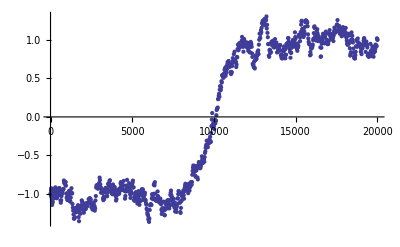

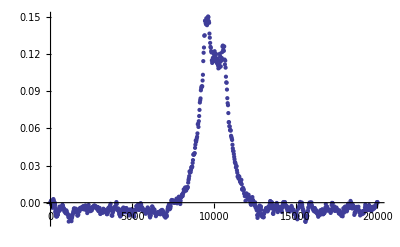

```mathematica
dataTest=Import["/mnt/heimdall/git/TwoDimTubes/2WellTubes-T0.15-pos0001000.dat","Table"];
ListPlot[dataTest[[All,1]],MaxPlotPoints->1000,PlotRange->All]
dataTest=Import["/mnt/heimdall/git/TwoDimTubes/2WellTubes-T0.15-pos0002000.dat","Table"];
ListPlot[dataTest[[All,10]],MaxPlotPoints->1000,PlotRange->All]
```

```mathematica
ListPlot[dataTest[[All,10]],MaxPlotPoints->1000,PlotRange->All]
```

-Graphics-

```mathematica
Bxx[t_,SIGMA1_,SIGMA2_,SIGMA3_]:=(SIGMA1+(SIGMA2-SIGMA1)*Exp[-SIGMA3*(t-5.)^2])^2
```

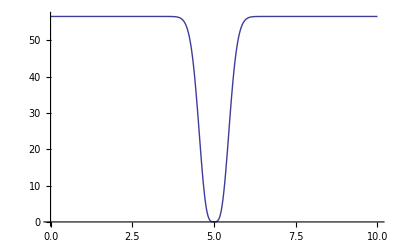

```mathematica
Plot[Bxx[t,7.52,0.10,5.20],{t,0,10},PlotRange->All]
```

```mathematica
bxxds2[t_,s1_,s2_,s3_]=D[Bxx[t,s1,s2,s3],s2]
```

2 ⅇ^(-s3 (-5.+t)^2) (s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2))

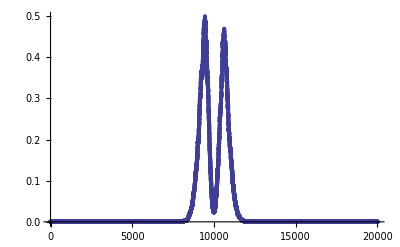

```mathematica
ListPlot[dataTest[[All,10]]*Table[bxxds2[t,7.52,0.1,5.2],{t,0,10,0.0005}],PlotRange->All]
```

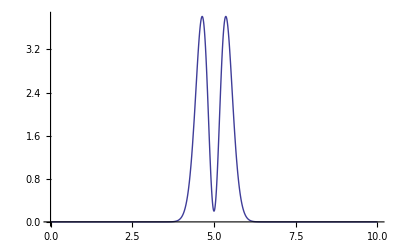

```mathematica
Plot[bxxds2[t,7.52,0.1,5.2],{t,0,10},PlotRange->All]
```

```mathematica
Sum[bxxds2[t,7.52,0.1,5.2],{t,0,10,0.0005}]
```

7067.79

```mathematica
Length[Table[bxxds2[t,1,0.1,5.2],{t,0,10,0.0005}]]
```

20001

```mathematica
bxxds2data=Partition[Flatten[Import["/mnt/heimdall/git/TwoDimTubes/out","Table"]],20001];
```

```mathematica
Dimensions[bxxds2data[[1]]]
```

{20001}

```mathematica
bxxds2data[1]
```

{{0.,0.0000506141,0.00011331,0.000194747,0.0000537181,0.0000109098,«19989»,-0.000166679,0.0000545315,0.000260905,0.0000642923,-0.0000363087,0.},{«1»}}[1]

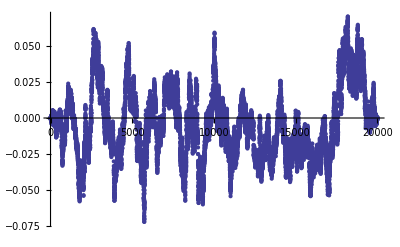

```mathematica
ListPlot[bxxds2data[[2]],PlotRange->All]
```

```mathematica
Total[bxxds2data*Table[bxxds2[t,1,0.1,5.2],{t,0,10,0.0005}]]
```

-9.64457

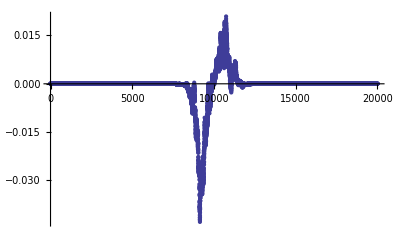

```mathematica
ListPlot[bxxds2data*Table[bxxds2[t,1,0.1,5.2],{t,0,10,0.0005}],PlotRange->All]
```

## Testing Steepest Descent constant B

```mathematica
dataTest=Import["/mnt/heimdall/git/TwoDimTubes/2WellTubes-T0.15-pos0010000.dat","Table"];
```

```mathematica
Dimensions[dataTest]
```

{20001,12}

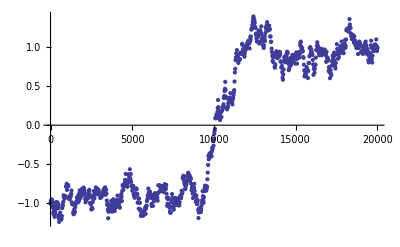
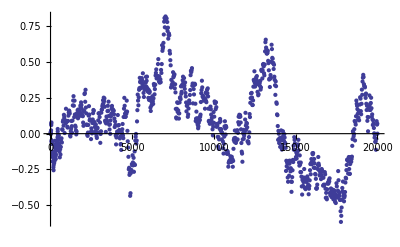
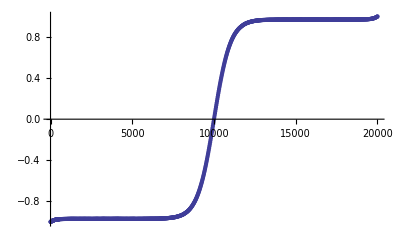
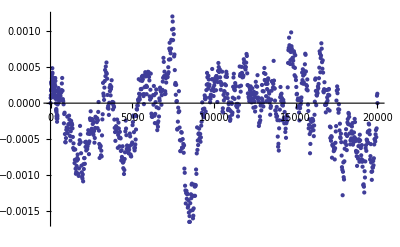
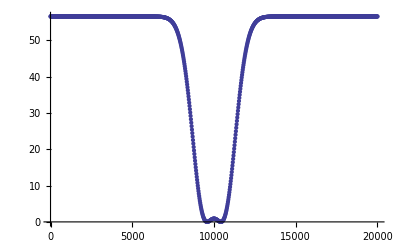
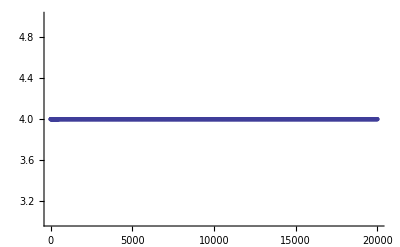
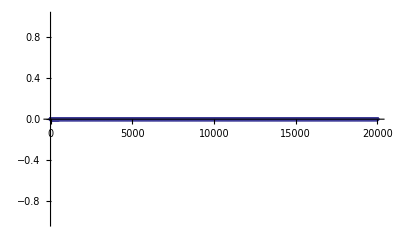
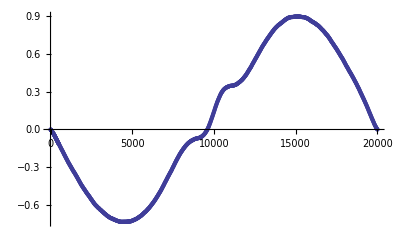

```mathematica
Table[ListPlot[dataTest[[All,i]],MaxPlotPoints->1000,PlotRange->All],{i,1,12}]
```

```mathematica
ListPlot[dataTest[[All,10]],MaxPlotPoints->1000,PlotRange->All]
```

-Graphics-

```mathematica
Bxx[t_,SIGMA1_,SIGMA2_,SIGMA3_]:=(SIGMA1+(SIGMA2-SIGMA1)*Exp[-SIGMA3*(t-5.)^2])^2
```

```mathematica
bxxds2[t_,s1_,s2_,s3_]=D[Bxx[t,s1,s2,s3],s2]
```

2 ⅇ^(-s3 (-5.+t)^2) (s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2))

```mathematica
bxxds1[t_,s1_,s2_,s3_]=D[Bxx[t,s1,s2,s3],s1]
```

2 (1-ⅇ^(-s3 (-5.+t)^2)) (s1+ⅇ^(-s3 (-5.+t)^2) (-s1+s2))

```mathematica
Total[dataTest[[All,10]]*Table[bxxds2[t,7.52,3,5.2],{t,0,10,0.0005}]]*0.0005
```

0.35113

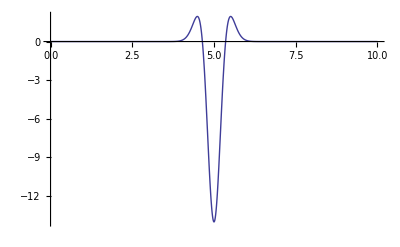

```mathematica
Plot[bxxds2[t,7.52,-7,5.2],{t,0,10},PlotRange->All]
```

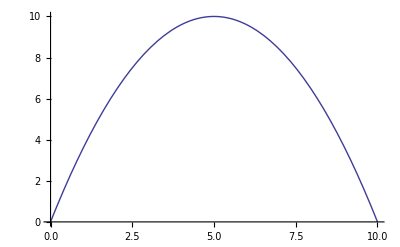

```mathematica
Plot[4t*(10-t)/10,{t,0,10}]
```

## ksdfgjh

```mathematica
data=Import["/mnt/heimdall/git/TwoDimTubesOneWell/2WellTubes-T0.15-pos0001000.dat","Table"];
```

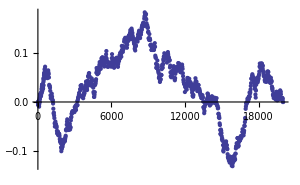
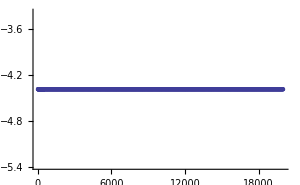
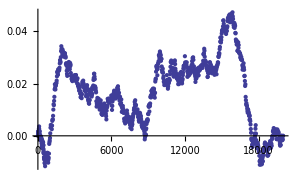

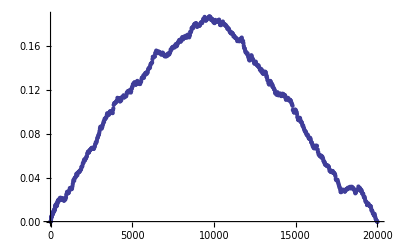

```mathematica
Table[ListPlot[data[[All,i]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300],{i,8,10}]
ListPlot[data[[All,1+7]]-data[[All,2+7]]*data[[All,3+7]],PlotRange->All,MaxPlotPoints->1000]
```

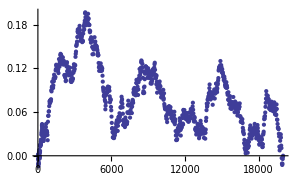
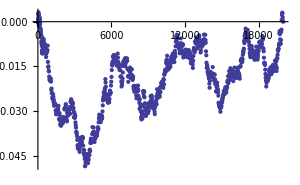
{-Graphics-,-Graphics-,-Graphics-}

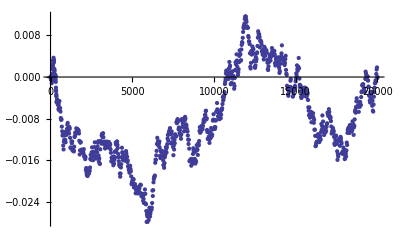

```mathematica
Table[ListPlot[data[[All,i]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300],{i,11,13}]
ListPlot[data[[All,1+10]]-data[[All,2+10]]*data[[All,3+10]],PlotRange->All,MaxPlotPoints->1000]
```

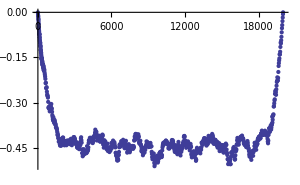
{-Graphics-,-Graphics-}

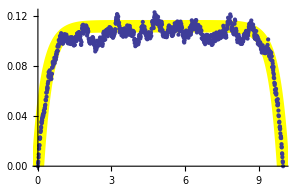

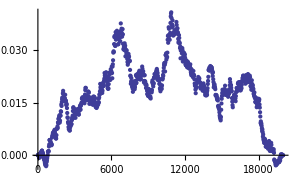

```mathematica
Table[ListPlot[data[[All,i]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300],{i,14,15}]
plt1=Plot[2 ϵ/A Sinh[A t] Sinh[A (T-t)]/Sinh[A T]/.{A->1.34,ϵ->0.15,T->10},{t,0,10},PlotRange->All,PlotStyle->{Thickness[.03],Yellow}];
timedata=Table[i,{i,0,10,0.0005}];
plt2=ListPlot[Transpose[{timedata,data[[All,16]]}],PlotRange->All,MaxPlotPoints->1000,ImageSize->500];
Show[plt1,plt2]
ListPlot[data[[All,1+13]]-data[[All,2+13]]*data[[All,3+13]],PlotRange->All,MaxPlotPoints->1000]
```

```mathematica
Table[ListPlot[data[[All,i]],PlotRange->All,MaxPlotPoints->1000,ImageSize->300],{i,14,15}]
plt1=Plot[2 ϵ/A Sinh[A t] Sinh[A (T-t)]/Sinh[A T]/.{A->1.34,ϵ->0.15,T->10},{t,0,10},PlotRange->All,PlotStyle->{Thickness[.03],Yellow}];
timedata=Table[i,{i,0,10,0.0005}];
plt2=ListPlot[Transpose[{timedata,data[[All,16]]}],PlotRange->All,MaxPlotPoints->1000,ImageSize->500];
Show[plt1,plt2]
ListPlot[data[[All,1+13]]-data[[All,2+13]]*data[[All,3+13]],PlotRange->All,MaxPlotPoints->1000]
```